## 136Nd - Petrache Study

## The 1-phonon structure (bands 3-4)

-Graphics-

According to Ref. “Evolution from y-soft to stable triaxiality in 136 Nd as a prerequisite of chirality”, the bands [3,4] are [L7, unknown]

```mathematica
ClearAll["Global`*"]
```

```mathematica
band3En=Sort[N[#/1000]&@{5841,4847,3995,3277}];
band4En=Sort[N[#/1000]&@{5346,4545,4026}];
band3Spins=Table[i,{i,10,16,2}];
band4Spins=Table[i,{i,11,15,2}];
```

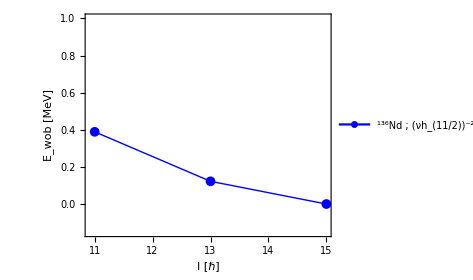

```mathematica
m1minipath="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/Nd-Nuclei/136Nd-1.pdf";
wobbling[yrast_,onephonon_,onespins_]:=Table[{onespins[[i]],onephonon[[i]]-1/2(yrast[[i]]+yrast[[i+1]])},{i,1,Length[onephonon]}];
data=wobbling[band3En,band4En,band4Spins];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{Style[Row[{Superscript["","136"],"Nd ; (νh_(11/2))^-2"}],FontFamily->"Times",30]},{0.5,0.85}],ImageSize->350,PlotRange->{Full,{-0.15,1}}];
Export[m1minipath,fig];
Show[fig]
```